# Geodesics Equation Solver

## Schwarzschild Spacetime

## Manual calculation of the geodesics equations

```mathematica
Clear["Global`*"]
ClearAll[r,θ,ϕ,t,s]



metric={{1/(1-(2 m)/r),0,0,0},{0,r^2,0,0},{0,0,r^2 Sin [θ]^2,0},{0,0,0,-(1-(2m)/r)}};

(*Eddington-Finkelstein coordinates*)
(*metric ={{0,0,0,1},{0,r^2,0,0},{0,0,r^2 Sin [θ]^2,0},{1,0,0,-(1-(2m)/r)}};*)

inversemetric = Simplify[Inverse[metric]];
coord={r,θ,ϕ,t};
christ[i_,j_,k_]:=christ[i,j,k]=Simplify[Sum[1/2 inversemetric[[i,d]] (D[metric[[d,k]],coord[[j]]]+D[metric[[d,j]],coord[[k]]]-D[metric[[j,k]],coord[[d]]]),{d,1,4}]]
```

```mathematica
eq=Table[coord[[i]]''+Sum[christ[i,j,k] coord[[j]]' coord[[k]]',{j,1,4},{k,1,4}],{i,1,4,1}];
eqs=eq/. {r''->r''[s],θ''->θ''[s],ϕ''->ϕ''[s],t''->t''[s],r'->r'[s],θ'->θ'[s],ϕ'->ϕ'[s],t'->t'[s],r->r[s],θ->θ[s],ϕ->ϕ[s],t->t[s]};
```

## Solving the equations

```mathematica
(*Initial conditions from E and L*)
initFromEL[E0_,L0_,r0_,th0_,m0_]:=Module[{f0,phDot,tDot,rDot,veff},
f0=1-(2m0)/r0;
phDot=L0/(r0^2 Sin[th0]^2);
tDot=E0/f0;
veff=f0 (1+L0^2/(r0^2 Sin[th0]^2));
rDot=-Sqrt[E0^2-veff];
{t[0]==0,r[0]==r0,θ[0]==th0,ϕ[0]==0,t'[0]==tDot,r'[0]==rDot,θ'[0]==0,ϕ'[0]==phDot}];


(*Numerical solve*)
En=1;L=3.465;r0=30;th0=Pi/3;m0=1;


initConds=initFromEL[En,L,r0,th0,m0];

EQ=Table[eqs[[i]]==0/. {m->m0},{i,1,4}];

Radius=2 ;
values ={};
sSingular=1000;
schwar=NDSolve[{EQ,initConds,
WhenEvent[r[s]<=0, "StopIntegration"]
},
{r,θ,ϕ,t},
{s,0,sSingular},
Method->{"StiffnessSwitching"},MaxStepSize->0.01,
AccuracyGoal->12,PrecisionGoal->12,
StepMonitor :> AppendTo[values,{r[s],θ[s],ϕ[s],t[s]}]
];

{rFunc,θFunc,ϕFunc,tFunc}={r,θ,ϕ,t}/. schwar[[1]];
domain=First@rFunc["Domain"]


trajectory=ParametricPlot3D[{rFunc[s] Sin[θFunc[s]] Cos[ϕFunc[s]],rFunc[s] Sin[θFunc[s]] Sin[ϕFunc[s]],rFunc[s] Cos[θFunc[s]]},{s,0,domain[[2]]},ColorFunction->Hue,AxesLabel->{"x","y","z"},PlotRange->{{-10,10},{-10,10},{-10,10}},RegionFunction->Function[{x,y,z,s},Sqrt[x^2+y^2+z^2]>10^-8],Exclusions->None];


horizon=SphericalPlot3D[Radius,{θ,0,Pi},{ϕ,0,2 Pi},PlotStyle->Directive[Gray,Opacity[0.3]]];

Show[trajectory,horizon]
```

{0.,1000.}

-Graphics3D-

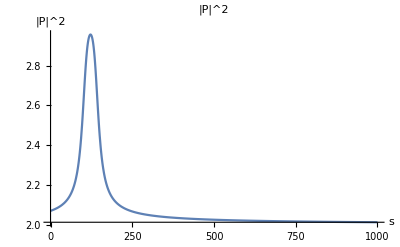

122.215

-Graphics3D-

112.559

```mathematica
(*Primer*)
U[s_]:={r'[s],θ'[s],ϕ'[s],t'[s]}/. schwar[[1]];
primer[s_]:=En*U[s]-{1,0,0,0};  (*Kronecker delta:only r component gets-1*)
(*P2[s_] :=Sum[metric[[mu,nu]]*primer[s][[mu]]*primer[s][[nu]],{mu,1,4},{nu,1,4}] /. {r->rFunc[s],θ->θFunc[s], m->m0};*)
P2[s_] := metric[[1,1]]+En^2/. {r->rFunc[s],θ->θFunc[s], m->m0};
primerPlot=Plot[P2[s],{s,0,domain[[2]]},PlotLabel->"|P|^2",PlotRange->All,AxesLabel->{"s","|P|^2"}]
sMax=NArgMax[{P2[s],0<=s<=domain[[2]]},s];
sMax
maxPmag=Sqrt[P2[sMax]];

maxPoint={rFunc[sMax] Sin[θFunc[sMax]] Cos[ϕFunc[sMax]],rFunc[sMax] Sin[θFunc[sMax]] Sin[ϕFunc[sMax]],rFunc[sMax] Cos[θFunc[sMax]]};

marker=Graphics3D[{Red,Sphere[maxPoint,0.3]}];

Show[trajectory,horizon,marker]
```

```mathematica
U0=U[sMax];
(*F0 from orthogonalaty and spacelike equations*)
f := 1-2 m0/r0
F0 = {0,0,√((f^-1-1)f^-1),1/r0 √(f^-1-1)};

phi=0.05;
U1=Cosh[phi]*U0+Sinh[phi]*F0;

newInit={
r[sMax]==rFunc[sMax],θ[sMax]==θFunc[sMax],ϕ[sMax]==ϕFunc[sMax],t[sMax]==tFunc[sMax],
r'[sMax]==U1[[1]],θ'[sMax]==U1[[2]],ϕ'[sMax]==U1[[3]],t'[sMax]==U1[[4]]};

(*Reintegrate post-burn geodesic*)
postBurn=NDSolve[Join[EQ,newInit],{r,θ,ϕ,t},{s,sMax,sMax+200},MaxSteps->Infinity][[1]];

{rPost,θPost,ϕPost}={r,θ,ϕ}/. postBurn;

trajectoryPre=ParametricPlot3D[{rFunc[s] Sin[θFunc[s]] Cos[ϕFunc[s]],rFunc[s] Sin[θFunc[s]] Sin[ϕFunc[s]],rFunc[s] Cos[θFunc[s]]},{s,0,sMax},PlotStyle->{Blue},PlotRange->{{-10,10},{-10,10},{-10,10}},AxesLabel->{"x","y","z"}];

trajectoryPost=ParametricPlot3D[{rPost[s] Sin[θPost[s]] Cos[ϕPost[s]],rPost[s] Sin[θPost[s]] Sin[ϕPost[s]],rPost[s] Cos[θPost[s]]},{s,sMax,sMax+200},PlotStyle->{Red}];

Show[trajectoryPre,trajectoryPost,marker,horizon]

E1=Cosh[phi]+Sinh[phi] √((2m0)/r0);
η = E1/En; η
```

-Graphics3D-

1.01417

```mathematica
(*Diagonostic Plots*)
tschwarFunc[s_]:=tFunc[s]-(rFunc[s]+2*Log[Abs[(rFunc[s]/2) -1]])
ts=Range[First@tFunc["Domain"][[1]],Last@tFunc["Domain"][[1]],0.01];

trPairs=Table[{tschwarFunc[s],rFunc[s]},{s,ts}];

rOfT=Interpolation[trPairs];

Plot[rOfT[t],{t,trPairs[[1,1]],trPairs[[-1,1]]},AxesLabel->{"t (Schwarzschild)","r"},PlotRange->All]


(*Plot[{rFunc[s],θFunc[s],ϕFunc[s],tFunc[s]},
{s,0,domain[[2]]},
PlotLegends->{"r","θ","ϕ","t"},PlotStyle->{Blue,Yellow,Green,Red},AxesLabel->{"s","x^i"}]*)

(*
ListLinePlot[values[[All,1]],PlotRange->All,AxesLabel->{"s","r"}]
ListLinePlot[values[[All,2]],PlotRange->All,AxesLabel->{"s","θ"}]
ListLinePlot[values[[All,3]],PlotRange->All,AxesLabel->{"s","ϕ"}]
ListLinePlot[values[[All,4]],PlotRange->All,AxesLabel->{"s","t"}]
*)
```